## Attenuators in both the arms of Mach-Zehnder

## Setup

#### Beam splitter transformation

```mathematica
B[r_,t_]={{t,-r},{r,t}};
```

```mathematica
(* Creation operators are representated by c *)
```

#### First beam splitter

```mathematica
{ca0,cb0}=B[1/(√2),1/(√2)].{ca1,cb1};
```

#### Phase shift in lower path

```mathematica
cb1=ⅇ^(-ⅈ ϕ)cb2;
```

#### Second and ‘Fourth’ beam splitters

```mathematica
{ca1,cc1}=B[𝓇,𝓉].{ca2,cc2};
{cb2,cd1}=B[𝓇,𝓉].{cb3,cd2};
```

#### Third beam splitter

```mathematica
{cc2,cd2}=B[1/(√2),1/(√2)].{cc3,cd3};
```

## 1. Single-Mode Squeezed Vacuum

### SMSV in mode a

```mathematica
ClearAll[S,out]
S[ξ_,n_]=1/(√Cosh[ξ])∑_(k=0)^n √Binomial[2k,k](-Tanh[ξ]/2)^k ca0^(2k)/(√((2k)!)); (* Source: Wikipedia*)
(* S[ξ,n] approximates single mode squeezed vacuum up to photon number = 2n *)
out[ca2_,cb3_,n_]=S[ξ,n];
Prob[n_,ξ_]=Sech[ξ]∑_(k=0)^n Binomial[2k,k](Tanh[ξ]/2)^(2k);
```

### Result (BS1,3 are 50-50 beam splitters and we post select on modes a and b having vacuum)

```mathematica
cof=CoefficientList[Expand[out[ca2,cb3,2]],{ca2,cb3}];
cof2=CoefficientList[Collect[Simplify[cof[[1,1]]],{cc3,cd3}],{cc3,cd3}];
Simplify[cof2[[1,1]]]
{Simplify[cof2[[2,1]]],Simplify[cof2[[1,2]]]}
Simplify[cof2[[2,2]]]
{Simplify[cof2[[3,1]]],Simplify[cof2[[1,3]]]}
Simplify[cof2[[3,3]]]
```

1/(√Cosh[ξ])

{0,0}

(ⅇ^(-2 ⅈ ϕ) (-1+ⅇ^(2 ⅈ ϕ)) 𝓇^2 Sinh[ξ])/(4 Cosh[ξ]^(3/2))

{-(ⅇ^(-2 ⅈ ϕ) (-1+ⅇ^(ⅈ ϕ))^2 𝓇^2 Sinh[ξ])/(8 Cosh[ξ]^(3/2)),-(ⅇ^(-2 ⅈ ϕ) (1+ⅇ^(ⅈ ϕ))^2 𝓇^2 Sinh[ξ])/(8 Cosh[ξ]^(3/2))}

(3 ⅇ^(-4 ⅈ ϕ) (-1+ⅇ^(2 ⅈ ϕ))^2 𝓇^4 Sinh[ξ]^2)/(64 Cosh[ξ]^(5/2))

So the output state is

1/(√Cosh[ξ])0,0
+ ((ⅇ^(-2 ⅈ ϕ) (-1+ⅇ^(2 ⅈ ϕ)) 𝓇^2 Sinh[ξ])/(4 Cosh[ξ]^(3/2)))1,1
+ √2(-(ⅇ^(-2 ⅈ ϕ) (-1+ⅇ^(ⅈ ϕ))^2 𝓇^2 Sinh[ξ])/(8 Cosh[ξ]^(3/2)))2,0
+√2(-(ⅇ^(-2 ⅈ ϕ) (1+ⅇ^(ⅈ ϕ))^2 𝓇^2 Sinh[ξ])/(8 Cosh[ξ]^(3/2)))0,2
+2((3 ⅇ^(-4 ⅈ ϕ) (-1+ⅇ^(2 ⅈ ϕ))^2 𝓇^4 Sinh[ξ]^2)/(64 Cosh[ξ]^(5/2)))2,2
+ …

### Observing interference with and without postselection on modes a and b

#### c=1,d=1

```mathematica
ClearAll[n,a,b,c,d,wopostselect,wpostselect]
n=5;  (* Squeezed states approximated with 2n terms *)
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
c=1; (* amplitude for mode c chosen to observe the interference  *)
d=1;(* amplitude for mode d chosen to observe the interference  *)
wopostselect[ϕ_,𝓇_,ξ_] = Module[{coeffψ,coefftable},
𝓉=√(1-𝓇^2);
coeffψ =√(c!d!)CoefficientList[CoefficientList[out[ca,cb,n],{cc3,cd3}][[c+1,d+1]],{ca,cb}];
coefftable=Table[Abs[√((i-1)!   (j-1)!)coeffψ[[i,j]]]^2,{i,1,Dimensions[coeffψ][[1]]},{j,1,Dimensions[coeffψ][[2]]}];
Total[Total[coefftable]]/Prob[n,ξ]
];
wpostselect[ϕ_,𝓇_,ξ_]=Module[{},
𝓉=√(1-𝓇^2);
Abs[√(c!d! a!b!)CoefficientList[CoefficientList[out[ca,cb,n],{cc3,cd3}][[c+1,d+1]],{ca,cb}][[a+1,b+1]]]^2/Prob[n,ξ]
];
Vwo[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vw[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wpostselect[x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wpostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
(*Manipulate[Plot[{wopostselect [ϕ,𝓇,ξ],wpostselect[ϕ,𝓇,ξ]},{ϕ,0,2π},PlotLabel-> "Visibility (w/o , w ) postselection = ("<>ToString[Vwo[𝓇,ξ]]<>" , "<>ToString[Vw[𝓇,ξ]]<>")",AxesLabel-> {ϕ,P},PlotLegends->{"Without postselection","With postselection"},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},PlotStyle-> {Solid,Dashed},PlotRange->Full,ImageSize->Medium],{ξ,5,10,Appearance-> "Open"},{𝓇,0.1,1,Appearance-> "Open"}]*)
```

```mathematica
FindMaximum[{wopostselect[π/2,𝓇,ξ],0≤𝓇≤1&&0<ξ},{𝓇,0.5},{ξ,1}]
```

{0.0729491,{𝓇→0.609028,ξ→7.23793}}

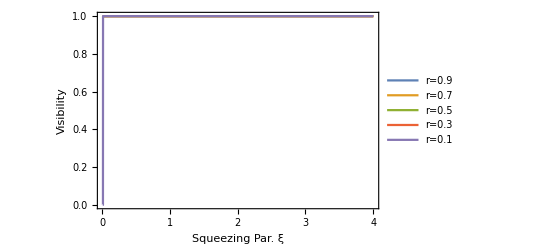

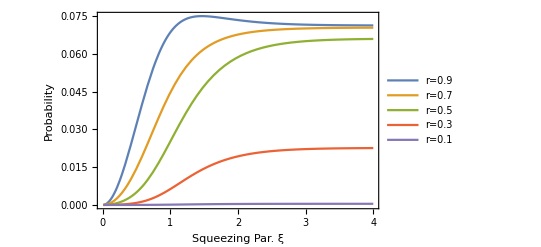

```mathematica
ClearAll[𝓇,ξ]
Plot[{Vwo[0.9,ξ],Vwo[0.7,ξ],Vwo[0.5,ξ],Vwo[0.3,ξ],Vwo[0.1,ξ]},{ξ,0.01,4},PlotRange->Full,Frame->True,FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopostselect[π/2,0.9,ξ],wopostselect[π/2,0.7,ξ],wopostselect[π/2,0.5,ξ],wopostselect[π/2,0.3,ξ],wopostselect[π/2,0.1,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.30]]
ClearAll[𝓇,ξ]
```

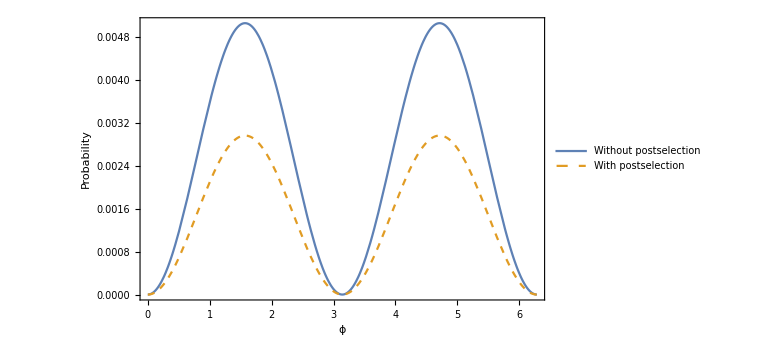

```mathematica
𝓇=0.5;
ξ=0.5;
Plot[{wopostselect[ϕ,𝓇,ξ],wpostselect[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwo[𝓇,ξ]]<>" , "<>ToString[Vw[𝓇,ξ]]<>") for 𝓇=0.5, ξ=1.462"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

#### c=2,d=2

```mathematica
ClearAll[n,a,b,c,d,wopostselect,wpostselect]
n=10;  (* Squeezed states approximated with 2n terms *)
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
c=2; (* amplitude for mode c chosen to observe the interference  *)
d=2;(* amplitude for mode d chosen to observe the interference  *)
wopostselect[ϕ_,𝓇_,ξ_] = Module[{coeffψ,coefftable},
𝓉=√(1-𝓇^2);
coeffψ =√(c!d!)CoefficientList[CoefficientList[out[ca,cb,n],{cc3,cd3}][[c+1,d+1]],{ca,cb}];
coefftable=Table[Abs[√((i-1)!   (j-1)!)coeffψ[[i,j]]]^2,{i,1,Dimensions[coeffψ][[1]]},{j,1,Dimensions[coeffψ][[2]]}];
Total[Total[coefftable]]/Prob[n,ξ]
];
wpostselect[ϕ_,𝓇_,ξ_]=Module[{},
𝓉=√(1-𝓇^2);
Abs[√(c!d! a!b!)CoefficientList[CoefficientList[out[ca,cb,n],{cc3,cd3}][[c+1,d+1]],{ca,cb}][[a+1,b+1]]]^2/Prob[n,ξ]
];
Vwo[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vw[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wpostselect[x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wpostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
(*Manipulate[Plot[{wopostselect [ϕ,𝓇,ξ],wpostselect[ϕ,𝓇,ξ]},{ϕ,0,2π},PlotLabel-> "Visibility (w/o , w ) postselection = ("<>ToString[Vwo[𝓇,ξ]]<>" , "<>ToString[Vw[𝓇,ξ]]<>")",AxesLabel-> {ϕ,P},PlotLegends->{"Without postselection","With postselection"},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},PlotStyle-> {Solid,Dashed},PlotRange->Full,ImageSize->Medium],{ξ,5,10,Appearance-> "Open"},{𝓇,0.1,1,Appearance-> "Open"}]*)
```

{0.0419302,{𝓇→1.,ξ→1.61082}}

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

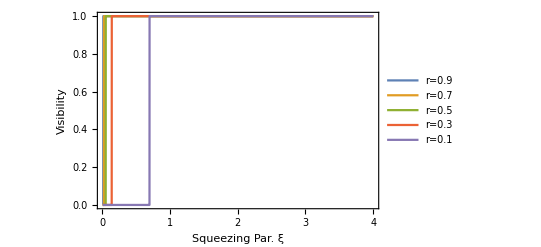

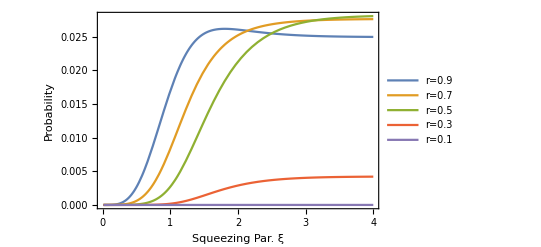

```mathematica
ClearAll[𝓇,ξ]
FindMaximum[{wopostselect[π/2,𝓇,ξ],0≤𝓇≤1&&0<ξ},{𝓇,0.5},{ξ,1}]
Plot[{Vwo[0.9,ξ],Vwo[0.7,ξ],Vwo[0.5,ξ],Vwo[0.3,ξ],Vwo[0.1,ξ]},{ξ,0.01,4},PlotRange->Full,Frame->True,FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopostselect[π/2,0.9,ξ],wopostselect[π/2,0.7,ξ],wopostselect[π/2,0.5,ξ],wopostselect[π/2,0.3,ξ],wopostselect[π/2,0.1,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.30]]
ClearAll[𝓇,ξ]
```

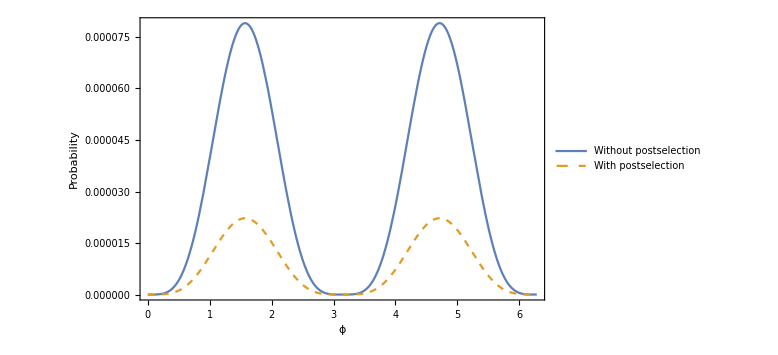

```mathematica
ClearAll[𝓇,ξ]
𝓇=0.5;
ξ=0.5;
Plot[{wopostselect[ϕ,𝓇,ξ],wpostselect[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwo[𝓇,ξ]]<>" , "<>ToString[Vw[𝓇,ξ]]<>") for 𝓇=0.5, ξ=1.462"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

## 2. Two-Mode Squeezed Vacuum Input and observing interference for P(1,1)

```mathematica
(* T[ξ_,n_]=1/Cosh[ξ]∑_(k=0)^n (-Tanh[ξ]/1)^k(ca0^k cb0^k)/(k!); (* Source: Wikipedia*)*)
(* T[ξ,n] approximates two mode squeezed vacuum up to photon number = n,n *)
ClearAll[out2,n]
n=5;
out2[ca2_,cb3_]=1/Cosh[ξ] Sum[(-Tanh[ξ]/1 ca0 cb0)^k/k!,{k,0,n}];
Prob[n_,ξ_]=Sech[ξ]^2(1-Tanh[ξ]^(2(n+1)))/(1-Tanh[ξ]^2);
```

```mathematica
(* Approximation of taking only a few terms *)
```

```mathematica
ClearAll[a,b,c,d,wopostselect2,wpostselect2]
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
c=1; (* amplitude for mode c chosen to observe the interference  *)
d=1;(* amplitude for mode d chosen to observe the interference  *)
wopostselect2[ϕ_,𝓇_,ξ_] = Module[{coeffψ,coefftable},
𝓉=√(1-𝓇^2);
coeffψ =√(c!d!)CoefficientList[CoefficientList[out2[ca,cb],{cc3,cd3}][[c+1,d+1]],{ca,cb}];
coefftable=Table[Abs[√((i-1)!   (j-1)!)coeffψ[[i,j]]]^2,{i,1,Dimensions[coeffψ][[1]]},{j,1,Dimensions[coeffψ][[2]]}];
Total[Total[coefftable]]/Prob[n,ξ]
];
wpostselect2[ϕ_,𝓇_,ξ_]=Module[{},
𝓉=√(1-𝓇^2);
Abs[√(c!d! a!b!)CoefficientList[CoefficientList[out2[ca,cb],{cc3,cd3}][[c+1,d+1]],{ca,cb}][[a+1,b+1]]]^2/Prob[n,ξ]
];
(* Visibility *)
Vwo2[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wopostselect2 [0,𝓇,ξ];
Imin =wopostselect2 [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vw2[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wpostselect2 [0,𝓇,ξ];
Imin =wpostselect2 [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
```

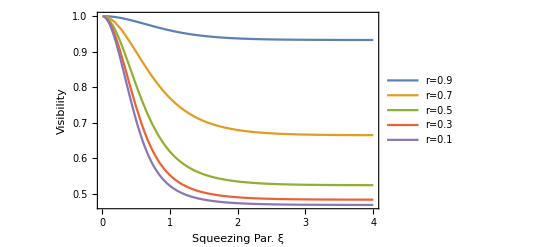

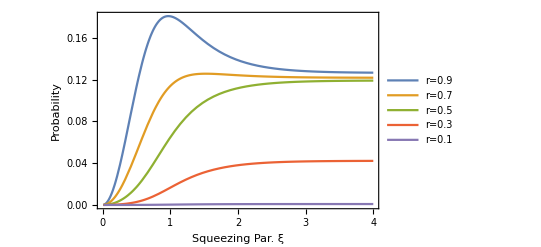

```mathematica
Plot[{Vwo2[0.9,ξ],Vwo2[0.7,ξ],Vwo2[0.5,ξ],Vwo2[0.32,ξ],Vwo2[0.1,ξ]},{ξ,0.01,4},PlotRange->Full,Frame->True,GridLines->{ {},{}},FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopostselect2[0,0.9,ξ],wopostselect2 [0,0.7,ξ],wopostselect2[0,0.5,ξ],wopostselect2[0,0.3,ξ],wopostselect2[0,0.1,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,GridLines-> {{},{}},ImageSize->Scaled[0.30]]
```

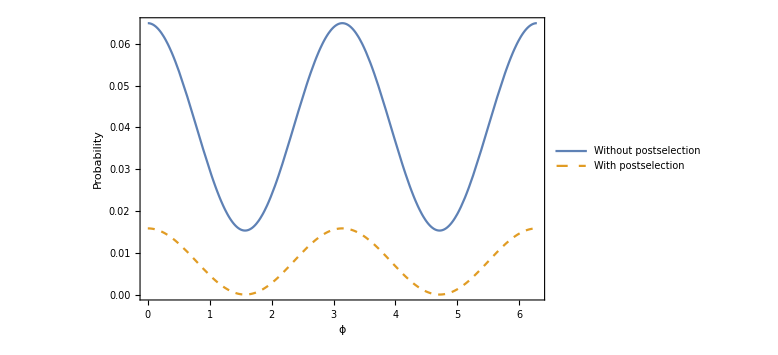

```mathematica
ClearAll[𝓇,ξ]
𝓇=0.5;
ξ=1;
Plot[{wopostselect2[ϕ,𝓇,ξ],wpostselect2[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwo2[𝓇,ξ]]<>" , "<>ToString[Vw2[𝓇,ξ]]<>")"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

## 3. Two-Mode Squeezed Vacuum Input and observing interference for P(coincidence w/o PNR) = P(not 0,not 0) = P(any,any)-P(0,any)-P(any,0)+P(0,0)

```mathematica
ClearAll[out4,n]
n=5;
outcoin[ca2_,cb3_]=1/Cosh[ξ] Sum[(-Tanh[ξ]/1 ca0 cb0)^k/k!,{k,0,n}];
Prob[n_,ξ_]=Sech[ξ]^2(1-Tanh[ξ]^(2(n+1)))/(1-Tanh[ξ]^2);
(* Approximation of taking only a few terms *)
ClearAll[wopscoin,wpscoin,a,b,c,d]
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
(*c=1; (* amplitude for mode c chosen to observe the interference  *)
d=1;(* amplitude for mode d chosen to observe the interference  *)*)
wopscoin[ϕ_,𝓇_,ξ_]=Module[{ψp,ψ,P},
𝓉=√(1-𝓇^2);
(*ψp=CoefficientList[out4[ca,cb],{cc3,cd3}];*)
ψp=CoefficientList[outcoin[ca,cb],{cc3,cd3,ca,cb}];
ψ =Table[√((k-1)!(l-1)!)ψp[[k,l]],{k,1,Dimensions[ψp][[1]]},{l,1,Dimensions[ψp][[2]]}];
P=Table[Total[Total[Table[Abs[√((i-1)!(j-1)!)ψ[[k,l]][[i,j]]]^2,{i,1,Dimensions[ψ[[k,l]]][[1]]},{j,1,Dimensions[ψ[[k,l]]][[2]]}]]],{k,1,Dimensions[ψ][[1]]},{l,1,Dimensions[ψ][[2]]}];
(Total[Total[P]]-Total[P,{1}][[1]]-Total[P,{2}][[1]]+P[[1,1]])/Prob[n,ξ]
];
```

```mathematica
wpscoin[ϕ_,𝓇_,ξ_]=Module[{ψp,ψ,P},
𝓉=√(1-𝓇^2);
ψp=CoefficientList[outcoin[ca,cb],{cc3,cd3,ca,cb}];
ψ =Table[√((k-1)!(l-1)!)ψp[[k,l]],{k,1,Dimensions[ψp][[1]]},{l,1,Dimensions[ψp][[2]]}];
P=Table[Abs[√(a!b!)ψ[[k,l]][[a+1,b+1]]]^2,{k,1,Dimensions[ψ][[1]]},{l,1,Dimensions[ψ][[2]]}];
(Total[Total[P]]-Total[P,{1}][[1]]-Total[P,{2}][[1]]+P[[1,1]])/Prob[n,ξ]
];
(* Visibility *)
Vwocoin[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wopscoin [0,𝓇,ξ];
Imin =wopscoin [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vwcoin[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wpscoin [0,𝓇,ξ];
Imin =wpscoin [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
```

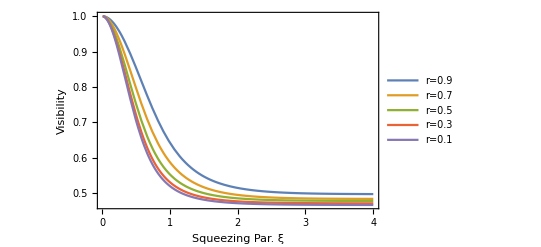

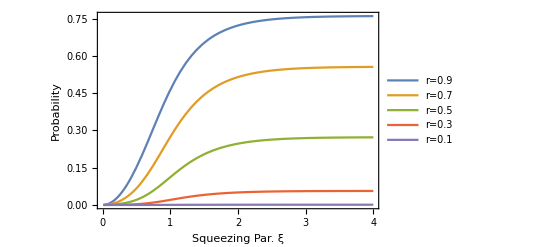

```mathematica
Plot[{Vwocoin[0.9,ξ],Vwocoin[0.7,ξ],Vwocoin[0.5,ξ],Vwocoin[0.3,ξ],Vwocoin[0.1,ξ]},{ξ,0.01,4},PlotRange->Full,GridLines->{{},{}},Frame->True,FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopscoin[0,0.9,ξ],wopscoin [0,0.7,ξ],wopscoin[0,0.5,ξ],wopscoin[0,0.3,ξ],wopscoin[0,0.1,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},GridLines->{{},{}},LabelStyle->Large,ImageSize->Scaled[0.30]]
```

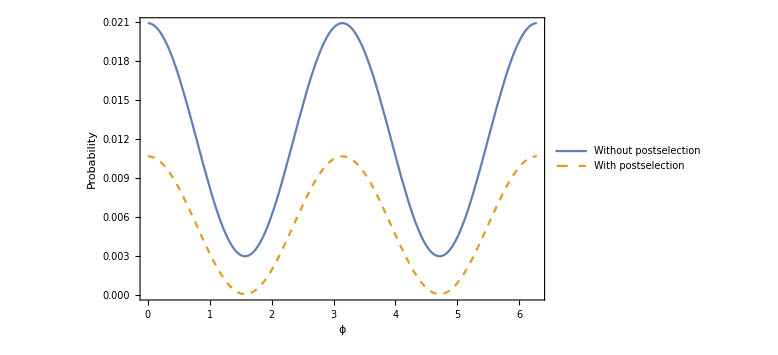

```mathematica
ClearAll[𝓇,ξ]
𝓇=0.5;
ξ=0.5;
Plot[{wopscoin[ϕ,𝓇,ξ],wpscoin[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwocoin[𝓇,ξ]]<>" , "<>ToString[Vwcoin[𝓇,ξ]]<>")"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

## Attenuators in the upper arm only

```mathematica
ClearAll[B,ca0,ca1,ca2,cb0,cb1,cb2,cb3,cc1,cc2,cc3,cd1,cd2,cd3]
```

## Setup

#### Beam splitter transformation

```mathematica
B[r_,t_]={{t,-r},{r,t}};
```

```mathematica
(* Creation operators are representated by c *)
```

#### First beam splitter

```mathematica
{ca0,cb0}=B[1/(√2),1/(√2)].{ca1,cb1};
```

#### Phase shift in lower path

```mathematica
cb1=ⅇ^(-ⅈ ϕ)cb2;
```

#### Second and ‘Fourth’ beam splitters

```mathematica
{ca1,cc1}=B[𝓇,𝓉].{ca2,cc2};
{cb2,cd1}=B[1,0].{cb3,cd2};
(* Fourth beamsplitter has been turned into a mirror*)
```

#### Third beam splitter

```mathematica
{cc2,cd2}=B[1/(√2),1/(√2)].{cc3,cd3};
```

## 1. Single-Mode Squeezed Vacuum

### SMSV in mode a

```mathematica
ClearAll[S,out]
S[ξ_,n_]=1/(√Cosh[ξ])∑_(k=0)^n √Binomial[2k,k](-Tanh[ξ]/2)^k ca0^(2k)/(√((2k)!)); (* Source: Wikipedia*)
(* S[ξ,n] approximates single mode squeezed vacuum up to photon number = 2n *)
out[ca2_,cb3_,n_]=S[ξ,n];
Prob[n_,ξ_]=Sech[ξ]∑_(k=0)^n Binomial[2k,k](Tanh[ξ]/2)^(2k);
```

### Observing interference with and without postselection on modes a and b

#### c=1,d=1

```mathematica
ClearAll[n,a,b,c,d,wopostselect,wpostselect]
n=5;  (* Squeezed states approximated with 2n terms *)
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
c=1; (* amplitude for mode c chosen to observe the interference  *)
d=1;(* amplitude for mode d chosen to observe the interference  *)
wopostselect[ϕ_,𝓇_,ξ_] = Module[{coeffψ,coefftable},
𝓉=√(1-𝓇^2);
coeffψ =√(c!d!)CoefficientList[CoefficientList[out[ca,cb,n],{cc3,cd3}][[c+1,d+1]],{ca,cb}];
coefftable=Table[Abs[√((i-1)!   (j-1)!)coeffψ[[i,j]]]^2,{i,1,Dimensions[coeffψ][[1]]},{j,1,Dimensions[coeffψ][[2]]}];
Total[Total[coefftable]]/Prob[n,ξ]
];
wpostselect[ϕ_,𝓇_,ξ_]=Module[{},
𝓉=√(1-𝓇^2);
Abs[√(c!d! a!b!)CoefficientList[CoefficientList[out[ca,cb,n],{cc3,cd3}][[c+1,d+1]],{ca,cb}][[a+1,b+1]]]^2/Prob[n,ξ]
];
Vwo[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vw[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wpostselect[x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wpostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
(*Manipulate[Plot[{wopostselect [ϕ,𝓇,ξ],wpostselect[ϕ,𝓇,ξ]},{ϕ,0,2π},PlotLabel-> "Visibility (w/o , w ) postselection = ("<>ToString[Vwo[𝓇,ξ]]<>" , "<>ToString[Vw[𝓇,ξ]]<>")",AxesLabel-> {ϕ,P},PlotLegends->{"Without postselection","With postselection"},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},PlotStyle-> {Solid,Dashed},PlotRange->Full,ImageSize->Medium],{ξ,5,10,Appearance-> "Open"},{𝓇,0.1,1,Appearance-> "Open"}]*)
```

```mathematica
FindMaximum[{wopostselect[π/2,𝓇,ξ],0≤𝓇≤1&&0<ξ},{𝓇,0.5},{ξ,1}]
```

{0.100669,{𝓇→1.,ξ→1.33327}}

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

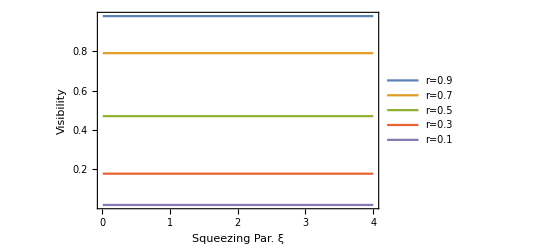

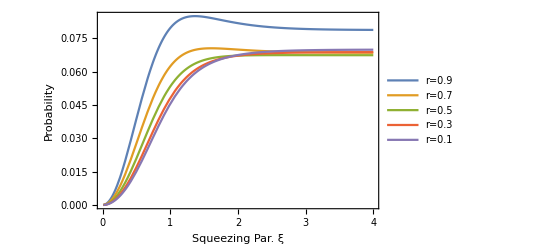

```mathematica
ClearAll[𝓇,ξ]
Plot[{Vwo[0.9,ξ],Vwo[0.7,ξ],Vwo[0.5,ξ],Vwo[0.3,ξ],Vwo[0.1,ξ]},{ξ,0.01,4},PlotRange->Full,Frame->True,FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopostselect[π/2,0.9,ξ],wopostselect[π/2,0.7,ξ],wopostselect[π/2,0.5,ξ],wopostselect[π/2,0.3,ξ],wopostselect[π/2,0.1,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.30]]
ClearAll[𝓇,ξ]
```

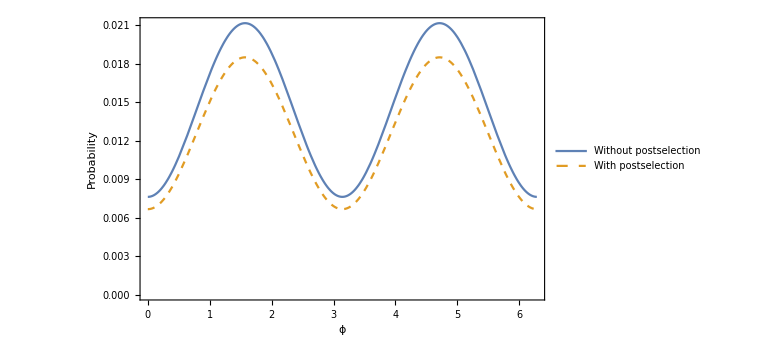

```mathematica
𝓇=0.5;
ξ=0.5;
Plot[{wopostselect[ϕ,𝓇,ξ],wpostselect[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwo[𝓇,ξ]]<>" , "<>ToString[Vw[𝓇,ξ]]<>") for 𝓇=0.5, ξ=1.462"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

#### c=2,d=2

```mathematica
ClearAll[n,a,b,c,d,wopostselect,wpostselect]
n=10;  (* Squeezed states approximated with 2n terms *)
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
c=2; (* amplitude for mode c chosen to observe the interference  *)
d=2;(* amplitude for mode d chosen to observe the interference  *)
Prob[n_,ξ_]=Sech[ξ]∑_(k=0)^n Binomial[2k,k](Tanh[ξ]/2)^(2k);
wopostselect[ϕ_,𝓇_,ξ_] = Module[{coeffψ,coefftable},
𝓉=√(1-𝓇^2);
coeffψ =√(c!d!)CoefficientList[CoefficientList[out[ca,cb,n],{cc3,cd3}][[c+1,d+1]],{ca,cb}];
coefftable=Table[Abs[√((i-1)!   (j-1)!)coeffψ[[i,j]]]^2,{i,1,Dimensions[coeffψ][[1]]},{j,1,Dimensions[coeffψ][[2]]}];
Total[Total[coefftable]]/Prob[n,ξ]
];
wpostselect[ϕ_,𝓇_,ξ_]=Module[{},
𝓉=√(1-𝓇^2);
Abs[√(c!d! a!b!)CoefficientList[CoefficientList[out[ca,cb,n],{cc3,cd3}][[c+1,d+1]],{ca,cb}][[a+1,b+1]]]^2/Prob[n,ξ]
];
Vwo[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vw[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wpostselect[x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wpostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
(*Manipulate[Plot[{wopostselect [ϕ,𝓇,ξ],wpostselect[ϕ,𝓇,ξ]},{ϕ,0,2π},PlotLabel-> "Visibility (w/o , w ) postselection = ("<>ToString[Vwo[𝓇,ξ]]<>" , "<>ToString[Vw[𝓇,ξ]]<>")",AxesLabel-> {ϕ,P},PlotLegends->{"Without postselection","With postselection"},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},PlotStyle-> {Solid,Dashed},PlotRange->Full,ImageSize->Medium],{ξ,5,10,Appearance-> "Open"},{𝓇,0.1,1,Appearance-> "Open"}]*)
```

{0.0419302,{𝓇→0.999999,ξ→1.61082}}

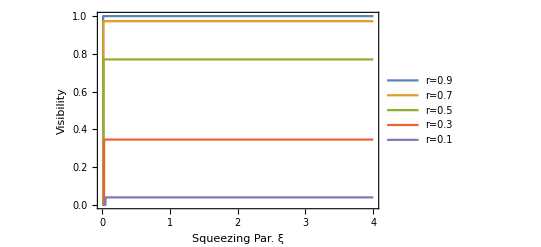

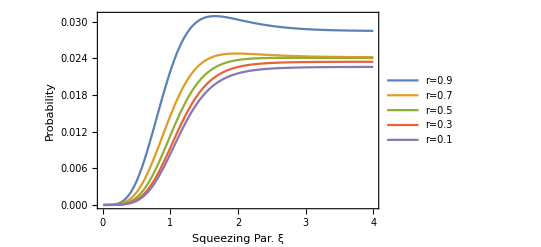

```mathematica
ClearAll[𝓇,ξ]
FindMaximum[{wopostselect[π/2,𝓇,ξ],0≤𝓇≤1&&0<ξ},{𝓇,0.5},{ξ,1}]
Plot[{Vwo[0.9,ξ],Vwo[0.7,ξ],Vwo[0.5,ξ],Vwo[0.3,ξ],Vwo[0.1,ξ]},{ξ,0.01,4},PlotRange->Full,Frame->True,FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopostselect[π/2,0.9,ξ],wopostselect[π/2,0.7,ξ],wopostselect[π/2,0.5,ξ],wopostselect[π/2,0.3,ξ],wopostselect[π/2,0.1,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.30]]
ClearAll[𝓇,ξ]
```

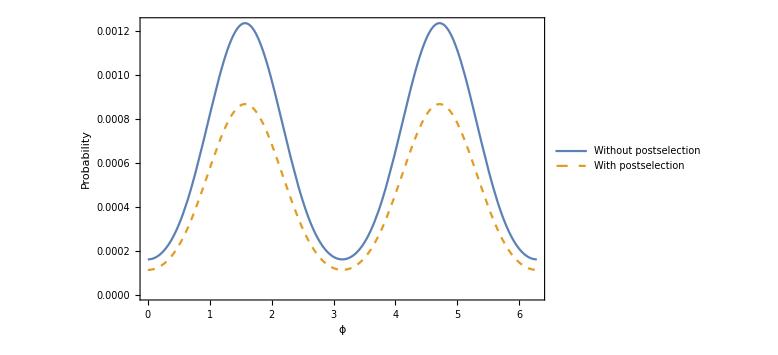

```mathematica
ClearAll[𝓇,ξ]
𝓇=0.5;
ξ=0.5;
Plot[{wopostselect[ϕ,𝓇,ξ],wpostselect[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwo[𝓇,ξ]]<>" , "<>ToString[Vw[𝓇,ξ]]<>") for 𝓇=0.5, ξ=1.462"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

## 2. Two-Mode Squeezed Vacuum Input and observing interference for P(1,1)

```mathematica
(* T[ξ_,n_]=1/Cosh[ξ]∑_(k=0)^n (-Tanh[ξ]/1)^k(ca0^k cb0^k)/(k!); (* Source: Wikipedia*)*)
(* T[ξ,n] approximates two mode squeezed vacuum up to photon number = n,n *)
ClearAll[out2,n]
n=5;
out2[ca2_,cb3_]=1/Cosh[ξ] Sum[(-Tanh[ξ]/1 ca0 cb0)^k/k!,{k,0,n}];
Prob[n_,ξ_]=Sech[ξ]^2(1-Tanh[ξ]^(2(n+1)))/(1-Tanh[ξ]^2);
```

```mathematica
(* Approximation of taking only a few terms *)
```

```mathematica
ClearAll[a,b,c,d,wopostselect2,wpostselect2]
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
c=1; (* amplitude for mode c chosen to observe the interference  *)
d=1;(* amplitude for mode d chosen to observe the interference  *)
wopostselect2[ϕ_,𝓇_,ξ_] = Module[{coeffψ,coefftable},
𝓉=√(1-𝓇^2);
coeffψ =√(c!d!)CoefficientList[CoefficientList[out2[ca,cb],{cc3,cd3}][[c+1,d+1]],{ca,cb}];
coefftable=Table[Abs[√((i-1)!   (j-1)!)coeffψ[[i,j]]]^2,{i,1,Dimensions[coeffψ][[1]]},{j,1,Dimensions[coeffψ][[2]]}];
Total[Total[coefftable]]/Prob[n,ξ]
];
wpostselect2[ϕ_,𝓇_,ξ_]=Module[{},
𝓉=√(1-𝓇^2);
Abs[√(c!d! a!b!)CoefficientList[CoefficientList[out2[ca,cb],{cc3,cd3}][[c+1,d+1]],{ca,cb}][[a+1,b+1]]]^2/Prob[n,ξ]
];
(* Visibility *)
Vwo2[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wopostselect2 [0,𝓇,ξ];
Imin =wopostselect2 [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vw2[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wpostselect2 [0,𝓇,ξ];
Imin =wpostselect2 [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
```

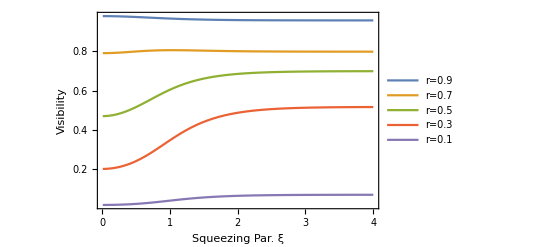

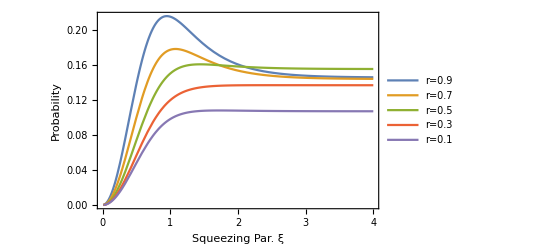

```mathematica
Plot[{Vwo2[0.9,ξ],Vwo2[0.7,ξ],Vwo2[0.5,ξ],Vwo2[0.32,ξ],Vwo2[0.1,ξ]},{ξ,0.01,4},PlotRange->Full,Frame->True,GridLines->{ {},{}},FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopostselect2[0,0.9,ξ],wopostselect2 [0,0.7,ξ],wopostselect2[0,0.5,ξ],wopostselect2[0,0.3,ξ],wopostselect2[0,0.1,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,GridLines-> {{},{}},ImageSize->Scaled[0.30]]
```

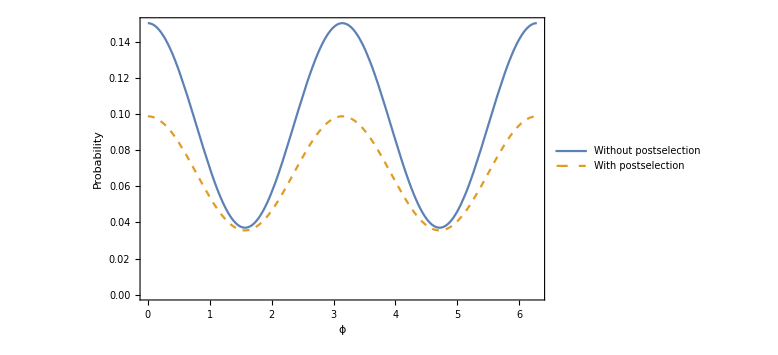

```mathematica
ClearAll[𝓇,ξ]
𝓇=0.5;
ξ=1;
Plot[{wopostselect2[ϕ,𝓇,ξ],wpostselect2[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwo2[𝓇,ξ]]<>" , "<>ToString[Vw2[𝓇,ξ]]<>")"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

## 3. Two-Mode Squeezed Vacuum Input and observing interference for P(coincidence w/o PNR) = P(not 0,not 0) = P(any,any)-P(0,any)-P(any,0)+P(0,0)

```mathematica
ClearAll[out4,n]
n=5;
outcoin[ca2_,cb3_]=1/Cosh[ξ] Sum[(-Tanh[ξ]/1 ca0 cb0)^k/k!,{k,0,n}];
Prob[n_,ξ_]=Sech[ξ]^2(1-Tanh[ξ]^(2(n+1)))/(1-Tanh[ξ]^2);
(* Approximation of taking only a few terms *)
ClearAll[wopscoin,wpscoin,a,b,c,d]
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
(*c=1; (* amplitude for mode c chosen to observe the interference  *)
d=1;(* amplitude for mode d chosen to observe the interference  *)*)
wopscoin[ϕ_,𝓇_,ξ_]=Module[{ψp,ψ,P},
𝓉=√(1-𝓇^2);
(*ψp=CoefficientList[out4[ca,cb],{cc3,cd3}];*)
ψp=CoefficientList[outcoin[ca,cb],{cc3,cd3,ca,cb}];
ψ =Table[√((k-1)!(l-1)!)ψp[[k,l]],{k,1,Dimensions[ψp][[1]]},{l,1,Dimensions[ψp][[2]]}];
P=Table[Total[Total[Table[Abs[√((i-1)!(j-1)!)ψ[[k,l]][[i,j]]]^2,{i,1,Dimensions[ψ[[k,l]]][[1]]},{j,1,Dimensions[ψ[[k,l]]][[2]]}]]],{k,1,Dimensions[ψ][[1]]},{l,1,Dimensions[ψ][[2]]}];
(Total[Total[P]]-Total[P,{1}][[1]]-Total[P,{2}][[1]]+P[[1,1]])/Prob[n,ξ]
];
```

```mathematica
wpscoin[ϕ_,𝓇_,ξ_]=Module[{ψp,ψ,P},
𝓉=√(1-𝓇^2);
ψp=CoefficientList[outcoin[ca,cb],{cc3,cd3,ca,cb}];
ψ =Table[√((k-1)!(l-1)!)ψp[[k,l]],{k,1,Dimensions[ψp][[1]]},{l,1,Dimensions[ψp][[2]]}];
P=Table[Abs[√(a!b!)ψ[[k,l]][[a+1,b+1]]]^2,{k,1,Dimensions[ψ][[1]]},{l,1,Dimensions[ψ][[2]]}];
(Total[Total[P]]-Total[P,{1}][[1]]-Total[P,{2}][[1]]+P[[1,1]])/Prob[n,ξ]
];
(* Visibility *)
Vwocoin[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wopscoin [0,𝓇,ξ];
Imin =wopscoin [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vwcoin[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wpscoin [0,𝓇,ξ];
Imin =wpscoin [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
```

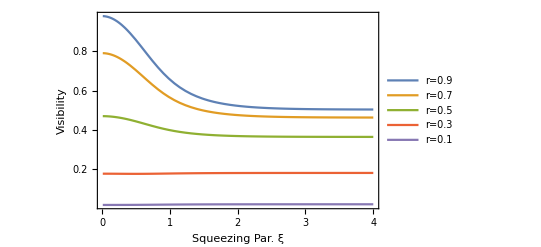

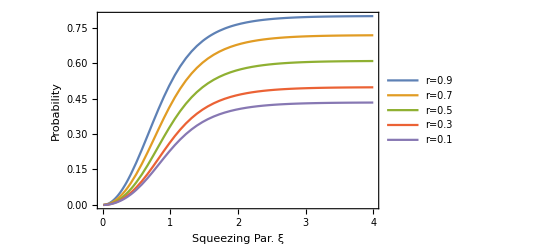

```mathematica
Plot[{Vwocoin[0.9,ξ],Vwocoin[0.7,ξ],Vwocoin[0.5,ξ],Vwocoin[0.3,ξ],Vwocoin[0.1,ξ]},{ξ,0.01,4},PlotRange->Full,GridLines->{{},{}},Frame->True,FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopscoin[0,0.9,ξ],wopscoin [0,0.7,ξ],wopscoin[0,0.5,ξ],wopscoin[0,0.3,ξ],wopscoin[0,0.1,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},GridLines->{{},{}},LabelStyle->Large,ImageSize->Scaled[0.30]]
```

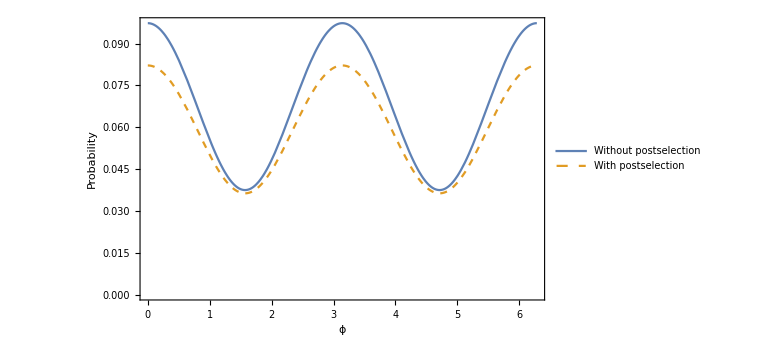

```mathematica
ClearAll[𝓇,ξ]
𝓇=0.5;
ξ=0.5;
Plot[{wopscoin[ϕ,𝓇,ξ],wpscoin[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwocoin[𝓇,ξ]]<>" , "<>ToString[Vwcoin[𝓇,ξ]]<>")"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

## Attenuators in both the arms of Mach-Zehnder (inefficient detectors)

## Setup

#### Beam splitter transformation

```mathematica
B[r_,t_]={{t,-r},{r,t}};
```

```mathematica
(* Creation operators are representated by c *)
```

#### First beam splitter

```mathematica
{ca0,cb0}=B[1/(√2),1/(√2)].{ca1,cb1};
```

#### Phase shift in lower path

```mathematica
cb1=ⅇ^(-ⅈ ϕ)cb2;
```

#### Second and ‘Fourth’ beam splitters

```mathematica
{ca1,cc1}=B[𝓇,𝓉].{ca2p,cc2};
{cb2,cd1}=B[𝓇,𝓉].{cb3p,cd2};
```

#### Fifth and Sixth beam splitters (to simulate inefficient detectors in modes a and b)

```mathematica
{ca2p,cadumpp}=B[𝓇loss,𝓉loss].{ca2,cadump};
{cb3p,cbdumpp}=B[𝓇loss,𝓉loss].{cb3,cbdump};
```

#### Third beam splitter

```mathematica
{cc2,cd2}=B[1/(√2),1/(√2)].{cc3,cd3};
```

```mathematica
𝓇loss=√(0.10/2);(*10% total loss of photons in both detectors, due to inefficiency *)
𝓉loss=√(1-𝓇loss^2);
```

## 1. Single-Mode Squeezed Vacuum

### SMSV in mode a

```mathematica
ClearAll[S,out]
S[ξ_,n_]=1/(√Cosh[ξ])∑_(k=0)^n √Binomial[2k,k](-Tanh[ξ]/2)^k ca0^(2k)/(√((2k)!)); (* Source: Wikipedia*)
(* S[ξ,n] approximates single mode squeezed vacuum up to photon number = 2n *)
out[ca2_,cb3_,n_]=S[ξ,n];
Prob[n_,ξ_]=Sech[ξ]∑_(k=0)^n Binomial[2k,k](Tanh[ξ]/2)^(2k);
```

### Observing interference with and without postselection on modes a and b

#### c=1,d=1

```mathematica
ClearAll[n,a,b,c,d,wopostselect,wpostselect]
n=5;  (* Squeezed states approximated with 2n terms *)
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
c=1; (* amplitude for mode c chosen to observe the interference  *)
d=1;(* amplitude for mode d chosen to observe the interference  *)

wopostselect[ϕ_,𝓇_,ξ_] = Module[{ψ,P},
𝓉=√(1-𝓇^2);
ψ =√(c!d!)CoefficientList[CoefficientList[out[ca,cb,n],{cc3,cd3}][[c+1,d+1]],{ca,cb,cadump,cbdump}];
P=Table[Abs[√((i-1)!   (j-1)!(k-1)!(l-1)!)ψ[[i,j,k,l]]]^2,{i,1,Dimensions[ψ][[1]]},{j,1,Dimensions[ψ][[2]]},{k,1,Dimensions[ψ][[3]]},{l,1,Dimensions[ψ][[4]]}];
Total[P,4]/Prob[n,ξ]
];
wpostselect[ϕ_,𝓇_,ξ_]=Module[{ψ,P},
𝓉=√(1-𝓇^2);
ψ=√(c!d! a!b!)CoefficientList[out[ca,cb,n],{cc3,cd3,ca,cb,cadump,cbdump}][[c+1,d+1,a+1,b+1]];
P=Table[Abs[√((k-1)!(l-1)!)ψ[[k,l]]]^2,{k,1,Dimensions[ψ][[1]]},{l,1,Dimensions[ψ][[2]]}];
Total[P,2]/Prob[n,ξ]
];
Vwo[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vw[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wpostselect[x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wpostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
```

```mathematica
ClearAll[𝓇,ξ]
Plot[{Vwo[0.9,ξ],Vwo[0.7,ξ],Vwo[0.5,ξ],Vwo[0.3,ξ],Vwo[0.1,ξ]},{ξ,0.01,4},PlotRange->Full,Frame->True,FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopostselect[π/2,0.9,ξ],wopostselect[π/2,0.7,ξ],wopostselect[π/2,0.5,ξ],wopostselect[π/2,0.3,ξ],wopostselect[π/2,0.1,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.30]]
ClearAll[𝓇,ξ]
```

-Graphics-

-Graphics-

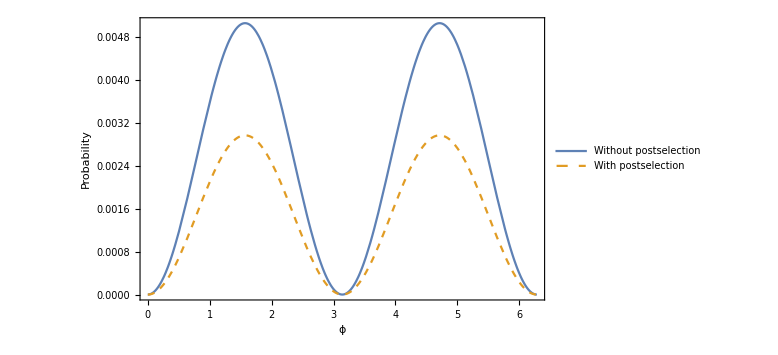

```mathematica
𝓇=0.5;
ξ=0.5;
Plot[{wopostselect[ϕ,𝓇,ξ],wpostselect[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwo[𝓇,ξ]]<>" , "<>ToString[Vw[𝓇,ξ]]<>") for 𝓇=0.5, ξ=1.462"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

#### c=2,d=2

```mathematica
ClearAll[n,a,b,c,d,wopostselect,wpostselect]
n=10;  (* Squeezed states approximated with 2n terms *)
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
c=2; (* amplitude for mode c chosen to observe the interference  *)
d=2;(* amplitude for mode d chosen to observe the interference  *)
wopostselect[ϕ_,𝓇_,ξ_] = Module[{ψ,P},
𝓉=√(1-𝓇^2);
ψ =√(c!d!)CoefficientList[CoefficientList[out[ca,cb,n],{cc3,cd3}][[c+1,d+1]],{ca,cb,cadump,cbdump}];
P=Table[Abs[√((i-1)!   (j-1)!(k-1)!(l-1)!)ψ[[i,j,k,l]]]^2,{i,1,Dimensions[ψ][[1]]},{j,1,Dimensions[ψ][[2]]},{k,1,Dimensions[ψ][[3]]},{l,1,Dimensions[ψ][[4]]}];
Total[P,4]/Prob[n,ξ]
];
wpostselect[ϕ_,𝓇_,ξ_]=Module[{ψ,P},
𝓉=√(1-𝓇^2);
ψ=√(c!d! a!b!)CoefficientList[out[ca,cb,n],{cc3,cd3,ca,cb,cadump,cbdump}][[c+1,d+1,a+1,b+1]];
P=Table[Abs[√((k-1)!(l-1)!)ψ[[k,l]]]^2,{k,1,Dimensions[ψ][[1]]},{l,1,Dimensions[ψ][[2]]}];
Total[P,2]/Prob[n,ξ]
];
Vwo[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vw[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wpostselect[x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wpostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
(*Manipulate[Plot[{wopostselect [ϕ,𝓇,ξ],wpostselect[ϕ,𝓇,ξ]},{ϕ,0,2π},PlotLabel-> "Visibility (w/o , w ) postselection = ("<>ToString[Vwo[𝓇,ξ]]<>" , "<>ToString[Vw[𝓇,ξ]]<>")",AxesLabel-> {ϕ,P},PlotLegends->{"Without postselection","With postselection"},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},PlotStyle-> {Solid,Dashed},PlotRange->Full,ImageSize->Medium],{ξ,5,10,Appearance-> "Open"},{𝓇,0.1,1,Appearance-> "Open"}]*)
```

```mathematica
ClearAll[𝓇,ξ]
FindMaximum[{wopostselect[π/2,𝓇,ξ],0≤𝓇≤1&&0<ξ},{𝓇,0.5},{ξ,1}]
Plot[{Vwo[0.9,ξ],Vwo[0.7,ξ],Vwo[0.5,ξ],Vwo[0.3,ξ],Vwo[0.1,ξ]},{ξ,0.01,4},PlotRange->Full,Frame->True,FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopostselect[π/2,0.9,ξ],wopostselect[π/2,0.7,ξ],wopostselect[π/2,0.5,ξ],wopostselect[π/2,0.3,ξ],wopostselect[π/2,0.1,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.30]]
ClearAll[𝓇,ξ]
```

{0.0419302,{𝓇→1.,ξ→1.61082}}

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

-Graphics-

-Graphics-

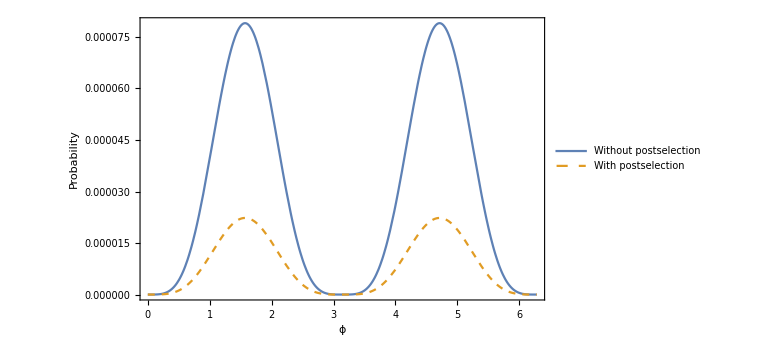

```mathematica
ClearAll[𝓇,ξ]
𝓇=0.5;
ξ=0.5;
Plot[{wopostselect[ϕ,𝓇,ξ],wpostselect[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwo[𝓇,ξ]]<>" , "<>ToString[Vw[𝓇,ξ]]<>") for 𝓇=0.5, ξ=1.462"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

## 2. Two-Mode Squeezed Vacuum Input and observing interference for P(1,1)

```mathematica
(* T[ξ_,n_]=1/Cosh[ξ]∑_(k=0)^n (-Tanh[ξ]/1)^k(ca0^k cb0^k)/(k!); (* Source: Wikipedia*)*)
(* T[ξ,n] approximates two mode squeezed vacuum up to photon number = n,n *)
ClearAll[out2,n]
n=5;
out2[ca2_,cb3_]=1/Cosh[ξ] Sum[(-Tanh[ξ]/1 ca0 cb0)^k/k!,{k,0,n}];
Prob[n_,ξ_]=Sech[ξ]^2(1-Tanh[ξ]^(2(n+1)))/(1-Tanh[ξ]^2);
```

```mathematica
(* Approximation of taking only a few terms *)
```

```mathematica
ClearAll[a,b,c,d,wopostselect2,wpostselect2]
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
c=1; (* amplitude for mode c chosen to observe the interference  *)
d=1;(* amplitude for mode d chosen to observe the interference  *)

wopostselect2[ϕ_,𝓇_,ξ_] = Module[{ψ,P},
𝓉=√(1-𝓇^2);
ψ =√(c!d!)CoefficientList[out2[ca,cb],{cc3,cd3,ca,cb,cadump,cbdump}][[c+1,d+1]];
P=Table[Abs[√((i-1)!   (j-1)!(k-1)!(l-1)!)ψ[[i,j,k,l]]]^2,{i,1,Dimensions[ψ][[1]]},{j,1,Dimensions[ψ][[2]]},{k,1,Dimensions[ψ][[3]]},{l,1,Dimensions[ψ][[4]]}];
Total[P,4]/Prob[n,ξ]
];
wpostselect2[ϕ_,𝓇_,ξ_]=Module[{ψ,P},
𝓉=√(1-𝓇^2);
ψ=√(c!d! a!b!)CoefficientList[out2[ca,cb],{cc3,cd3,ca,cb,cadump,cbdump}][[c+1,d+1,a+1,b+1]];
P=Table[Abs[√((k-1)!(l-1)!)ψ[[k,l]]]^2,{k,1,Dimensions[ψ][[1]]},{l,1,Dimensions[ψ][[2]]}];
Total[P,2]/Prob[n,ξ]
];

(* Visibility *)
Vwo2[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wopostselect2 [0,𝓇,ξ];
Imin =wopostselect2 [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vw2[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wpostselect2 [0,𝓇,ξ];
Imin =wpostselect2 [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
```

```mathematica
Plot[{Vwo2[0.9,ξ],Vwo2[0.7,ξ],Vwo2[0.5,ξ],Vwo2[0.32,ξ],Vwo2[0.1,ξ]},{ξ,0.01,4},PlotRange->Full,Frame->True,GridLines->{ {},{}},FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopostselect2[0,0.9,ξ],wopostselect2 [0,0.7,ξ],wopostselect2[0,0.5,ξ],wopostselect2[0,0.3,ξ],wopostselect2[0,0.1,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,GridLines-> {{},{}},ImageSize->Scaled[0.30]]
```

-Graphics-

-Graphics-

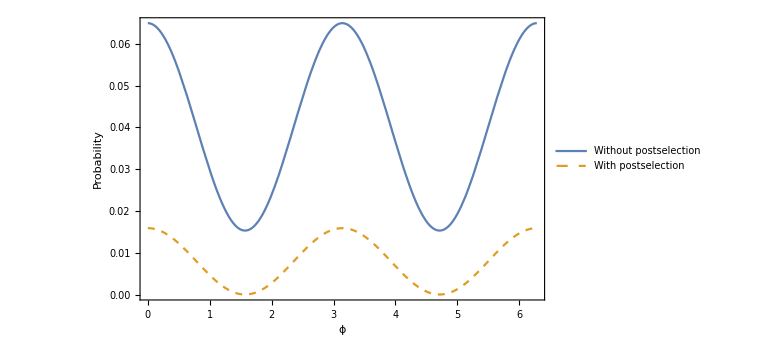

```mathematica
ClearAll[𝓇,ξ]
𝓇=0.5;
ξ=1;
Plot[{wopostselect2[ϕ,𝓇,ξ],wpostselect2[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwo2[𝓇,ξ]]<>" , "<>ToString[Vw2[𝓇,ξ]]<>")"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

## 3. Two-Mode Squeezed Vacuum Input and observing interference for P(coincidence w/o PNR) = P(not 0,not 0) = P(any,any)-P(0,any)-P(any,0)+P(0,0)

```mathematica
ClearAll[outcoin,n]
n=5;
outcoin[ca2_,cb3_]=1/Cosh[ξ] Sum[(-Tanh[ξ]/1 ca0 cb0)^k/k!,{k,0,n}];
(* Approximation of taking only a few terms *)
ClearAll[wopscoin,wpscoin,a,b,c,d]
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
(*c=1; (* amplitude for mode c chosen to observe the interference  *)
d=1;(* amplitude for mode d chosen to observe the interference  *)*)
Prob[n_,ξ_]=Sech[ξ]^2(1-Tanh[ξ]^(2(n+1)))/(1-Tanh[ξ]^2);
wopscoin[ϕ_,𝓇_,ξ_]=Module[{ψp,ψ,P},
𝓉=√(1-𝓇^2);
ψp=CoefficientList[outcoin[ca,cb],{cc3,cd3,ca,cb,cadump,cbdump}];
ψ =Table[√((i-1)!(j-1)!(k-1)!(l-1)!(g-1)!(h-1)!)ψp[[i,j,k,l,g,h]],{i,1,Dimensions[ψp][[1]]},{j,1,Dimensions[ψp][[2]]},{k,1,Dimensions[ψp][[3]]},{l,1,Dimensions[ψp][[4]]},{g,1,Dimensions[ψp][[5]]},{h,1,Dimensions[ψp][[6]]}];
P=Table[Total[Table[Abs[ψ[[i,j]][[k,l,g,h]]]^2,{k,1,Dimensions[ψ[[i,j]]][[1]]},{l,1,Dimensions[ψ[[i,j]]][[2]]},{g,1,Dimensions[ψ[[i,j]]][[3]]},{h,1,Dimensions[ψ[[i,j]]][[4]]}],4],{i,1,Dimensions[ψ][[1]]},{j,1,Dimensions[ψ][[2]]}];
(Total[P,2]-Total[P,{1}][[1]]-Total[P,{2}][[1]]+P[[1,1]])/Prob[n,ξ]
];
wpscoin[ϕ_,𝓇_,ξ_]=Module[{ψp,ψ,P},
𝓉=√(1-𝓇^2);
ψp=CoefficientList[outcoin[ca,cb],{cc3,cd3,ca,cb,cadump,cbdump}];
ψ =Table[√((i-1)!(j-1)!(k-1)!(l-1)!(g-1)!(h-1)!)ψp[[i,j,k,l,g,h]],{i,1,Dimensions[ψp][[1]]},{j,1,Dimensions[ψp][[2]]},{k,1,Dimensions[ψp][[3]]},{l,1,Dimensions[ψp][[4]]},{g,1,Dimensions[ψp][[5]]},{h,1,Dimensions[ψp][[6]]}];
P=Table[Total[Table[Abs[ψ[[i,j]][[a+1,b+1,g,h]]]^2,{g,1,Dimensions[ψ[[i,j]][[a+1,b+1]]][[1]]},{h,1,Dimensions[ψ[[i,j]][[a+1,b+1]]][[2]]}],2],{i,1,Dimensions[ψ][[1]]},{j,1,Dimensions[ψ][[2]]}];
(Total[P,2]-Total[P,{1}][[1]]-Total[P,{2}][[1]]+P[[1,1]])/Prob[n,ξ]
];
(* Visibility *)
Vwocoin[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wopscoin [0,𝓇,ξ];
Imin =wopscoin [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vwcoin[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wpscoin [0,𝓇,ξ];
Imin =wpscoin [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
```

$Aborted

```mathematica
Plot[{Vwocoin[0.9,ξ],Vwocoin[0.7,ξ],Vwocoin[0.5,ξ],Vwocoin[0.3,ξ],Vwocoin[0.1,ξ]},{ξ,0.01,4},PlotRange->Full,GridLines->{{},{}},Frame->True,FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopscoin[0,0.9,ξ],wopscoin [0,0.7,ξ],wopscoin[0,0.5,ξ],wopscoin[0,0.3,ξ],wopscoin[0,0.1,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},GridLines->{{},{}},LabelStyle->Large,ImageSize->Scaled[0.30]]
```

-Graphics-

-Graphics-

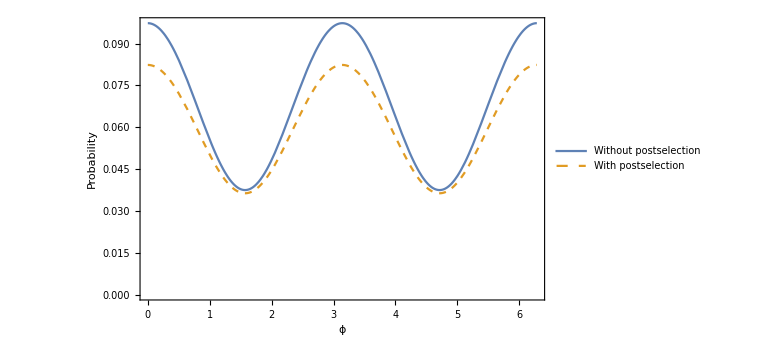

```mathematica
ClearAll[𝓇,ξ]
𝓇=0.5;
ξ=0.5;
Plot[{wopscoin[ϕ,𝓇,ξ],wpscoin[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwocoin[𝓇,ξ]]<>" , "<>ToString[Vwcoin[𝓇,ξ]]<>")"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

## Attenuators in the upper arm only (inefficient detectors)

## Setup

#### Beam splitter transformation

```mathematica
B[r_,t_]={{t,-r},{r,t}};
```

```mathematica
(* Creation operators are representated by c *)
```

#### First beam splitter

```mathematica
{ca0,cb0}=B[1/(√2),1/(√2)].{ca1,cb1};
```

#### Phase shift in lower path

```mathematica
cb1=ⅇ^(-ⅈ ϕ)cb2;
```

#### Second and ‘Fourth’ beam splitters

```mathematica
{ca1,cc1}=B[𝓇,𝓉].{ca2p,cc2};
{cb2,cd1}=B[1,0].{cb3p,cd2};
```

#### Fifth and Sixth beam splitters (to simulate inefficient detectors in modes a and b)

```mathematica
{ca2p,cadumpp}=B[𝓇loss,𝓉loss].{ca2,cadump};
{cb3p,cbdumpp}=B[𝓇loss,𝓉loss].{cb3,cbdump};
```

#### Third beam splitter

```mathematica
{cc2,cd2}=B[1/(√2),1/(√2)].{cc3,cd3};
```

```mathematica
𝓇loss=√(0.10/2);(*10% total loss of photons in both detectors, due to inefficiency *)
𝓉loss=√(1-𝓇loss^2);
```

## 1. Single-Mode Squeezed Vacuum

### SMSV in mode a

```mathematica
ClearAll[S,out]
S[ξ_,n_]=1/(√Cosh[ξ])∑_(k=0)^n √Binomial[2k,k](-Tanh[ξ]/2)^k ca0^(2k)/(√((2k)!)); (* Source: Wikipedia*)
(* S[ξ,n] approximates single mode squeezed vacuum up to photon number = 2n *)
out[ca2_,cb3_,n_]=S[ξ,n];
Prob[n_,ξ_]=Sech[ξ]∑_(k=0)^n Binomial[2k,k](Tanh[ξ]/2)^(2k);
```

### Observing interference with and without postselection on modes a and b

#### c=1,d=1

```mathematica
ClearAll[n,a,b,c,d,wopostselect,wpostselect]
n=5;  (* Squeezed states approximated with 2n terms *)
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
c=1; (* amplitude for mode c chosen to observe the interference  *)
d=1;(* amplitude for mode d chosen to observe the interference  *)

wopostselect[ϕ_,𝓇_,ξ_] = Module[{ψ,P},
𝓉=√(1-𝓇^2);
ψ =√(c!d!)CoefficientList[CoefficientList[out[ca,cb,n],{cc3,cd3}][[c+1,d+1]],{ca,cb,cadump,cbdump}];
P=Table[Abs[√((i-1)!   (j-1)!(k-1)!(l-1)!)ψ[[i,j,k,l]]]^2,{i,1,Dimensions[ψ][[1]]},{j,1,Dimensions[ψ][[2]]},{k,1,Dimensions[ψ][[3]]},{l,1,Dimensions[ψ][[4]]}];
Total[P,4]/Prob[n,ξ]
];
wpostselect[ϕ_,𝓇_,ξ_]=Module[{ψ,P},
𝓉=√(1-𝓇^2);
ψ=√(c!d! a!b!)CoefficientList[out[ca,cb,n],{cc3,cd3,ca,cb,cadump,cbdump}][[c+1,d+1,a+1,b+1]];
P=Table[Abs[√((k-1)!(l-1)!)ψ[[k,l]]]^2,{k,1,Dimensions[ψ][[1]]},{l,1,Dimensions[ψ][[2]]}];
Total[P,2]/Prob[n,ξ]
];
Vwo[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vw[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wpostselect[x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wpostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
```

```mathematica
ClearAll[𝓇,ξ]
Plot[{Vwo[0.9,ξ],Vwo[0.7,ξ],Vwo[0.5,ξ],Vwo[0.3,ξ],Vwo[0.1,ξ]},{ξ,0.01,4},PlotRange->Full,Frame->True,FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopostselect[π/2,0.9,ξ],wopostselect[π/2,0.7,ξ],wopostselect[π/2,0.5,ξ],wopostselect[π/2,0.3,ξ],wopostselect[π/2,0.1,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.30]]
ClearAll[𝓇,ξ]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

-Graphics-

-Graphics-

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

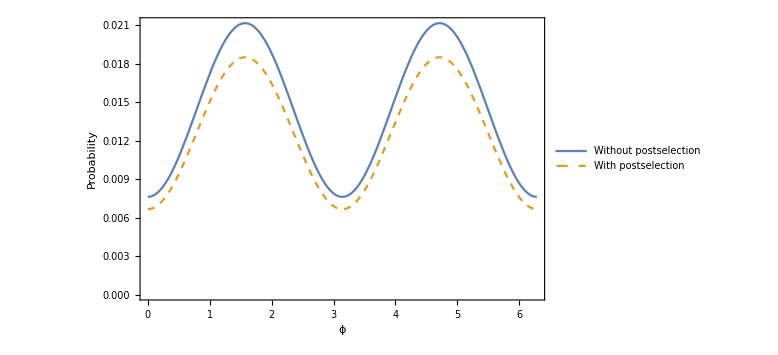

```mathematica
𝓇=0.5;
ξ=0.5;
Plot[{wopostselect[ϕ,𝓇,ξ],wpostselect[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwo[𝓇,ξ]]<>" , "<>ToString[Vw[𝓇,ξ]]<>") for 𝓇=0.5, ξ=1.462"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

#### c=2,d=2

```mathematica
ClearAll[n,a,b,c,d,wopostselect,wpostselect]
n=10;  (* Squeezed states approximated with 2n terms *)
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
c=2; (* amplitude for mode c chosen to observe the interference  *)
d=2;(* amplitude for mode d chosen to observe the interference  *)
wopostselect[ϕ_,𝓇_,ξ_] = Module[{ψ,P},
𝓉=√(1-𝓇^2);
ψ =√(c!d!)CoefficientList[CoefficientList[out[ca,cb,n],{cc3,cd3}][[c+1,d+1]],{ca,cb,cadump,cbdump}];
P=Table[Abs[√((i-1)!   (j-1)!(k-1)!(l-1)!)ψ[[i,j,k,l]]]^2,{i,1,Dimensions[ψ][[1]]},{j,1,Dimensions[ψ][[2]]},{k,1,Dimensions[ψ][[3]]},{l,1,Dimensions[ψ][[4]]}];
Total[P,4]/Prob[n,ξ]
];
wpostselect[ϕ_,𝓇_,ξ_]=Module[{ψ,P},
𝓉=√(1-𝓇^2);
ψ=√(c!d! a!b!)CoefficientList[out[ca,cb,n],{cc3,cd3,ca,cb,cadump,cbdump}][[c+1,d+1,a+1,b+1]];
P=Table[Abs[√((k-1)!(l-1)!)ψ[[k,l]]]^2,{k,1,Dimensions[ψ][[1]]},{l,1,Dimensions[ψ][[2]]}];
Total[P,2]/Prob[n,ξ]
];
Vwo[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vw[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wpostselect[x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wpostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
(*Manipulate[Plot[{wopostselect [ϕ,𝓇,ξ],wpostselect[ϕ,𝓇,ξ]},{ϕ,0,2π},PlotLabel-> "Visibility (w/o , w ) postselection = ("<>ToString[Vwo[𝓇,ξ]]<>" , "<>ToString[Vw[𝓇,ξ]]<>")",AxesLabel-> {ϕ,P},PlotLegends->{"Without postselection","With postselection"},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},PlotStyle-> {Solid,Dashed},PlotRange->Full,ImageSize->Medium],{ξ,5,10,Appearance-> "Open"},{𝓇,0.1,1,Appearance-> "Open"}]*)
```

{0.0329238,{𝓇→0.548607,ξ→6.44921}}

-Graphics-

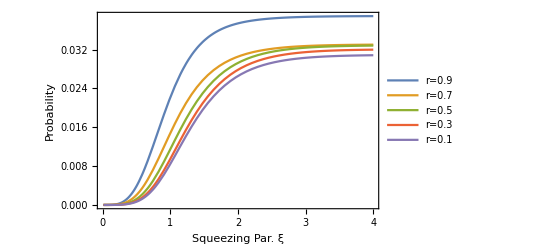

```mathematica
ClearAll[𝓇,ξ]
FindMaximum[{wopostselect[π/2,𝓇,ξ],0≤𝓇≤1&&0<ξ},{𝓇,0.5},{ξ,1}]
Plot[{Vwo[0.9,ξ],Vwo[0.7,ξ],Vwo[0.5,ξ],Vwo[0.3,ξ],Vwo[0.1,ξ]},{ξ,0.01,4},PlotRange->Full,Frame->True,FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopostselect[π/2,0.9,ξ],wopostselect[π/2,0.7,ξ],wopostselect[π/2,0.5,ξ],wopostselect[π/2,0.3,ξ],wopostselect[π/2,0.1,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.30]]
ClearAll[𝓇,ξ]
```

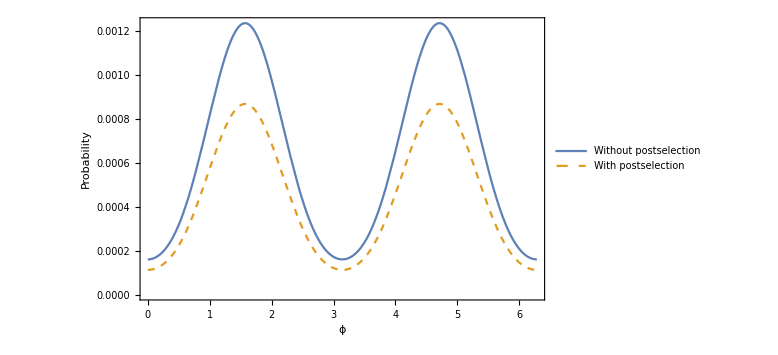

```mathematica
ClearAll[𝓇,ξ]
𝓇=0.5;
ξ=0.5;
Plot[{wopostselect[ϕ,𝓇,ξ],wpostselect[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwo[𝓇,ξ]]<>" , "<>ToString[Vw[𝓇,ξ]]<>") for 𝓇=0.5, ξ=1.462"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

## 2. Two-Mode Squeezed Vacuum Input and observing interference for P(1,1)

```mathematica
(* T[ξ_,n_]=1/Cosh[ξ]∑_(k=0)^n (-Tanh[ξ]/1)^k(ca0^k cb0^k)/(k!); (* Source: Wikipedia*)*)
(* T[ξ,n] approximates two mode squeezed vacuum up to photon number = n,n *)
ClearAll[out2,n]
n=5;
out2[ca2_,cb3_]=1/Cosh[ξ] Sum[(-Tanh[ξ]/1 ca0 cb0)^k/k!,{k,0,n}];
Prob[n_,ξ_]=Sech[ξ]^2(1-Tanh[ξ]^(2(n+1)))/(1-Tanh[ξ]^2);
```

```mathematica
(* Approximation of taking only a few terms *)
```

```mathematica
ClearAll[a,b,c,d,wopostselect2,wpostselect2]
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
c=1; (* amplitude for mode c chosen to observe the interference  *)
d=1;(* amplitude for mode d chosen to observe the interference  *)

wopostselect2[ϕ_,𝓇_,ξ_] = Module[{ψ,P},
𝓉=√(1-𝓇^2);
ψ =√(c!d!)CoefficientList[out2[ca,cb],{cc3,cd3,ca,cb,cadump,cbdump}][[c+1,d+1]];
P=Table[Abs[√((i-1)!   (j-1)!(k-1)!(l-1)!)ψ[[i,j,k,l]]]^2,{i,1,Dimensions[ψ][[1]]},{j,1,Dimensions[ψ][[2]]},{k,1,Dimensions[ψ][[3]]},{l,1,Dimensions[ψ][[4]]}];
Total[P,4]/Prob[n,ξ]
];
wpostselect2[ϕ_,𝓇_,ξ_]=Module[{ψ,P},
𝓉=√(1-𝓇^2);
ψ=√(c!d! a!b!)CoefficientList[out2[ca,cb],{cc3,cd3,ca,cb,cadump,cbdump}][[c+1,d+1,a+1,b+1]];
P=Table[Abs[√((k-1)!(l-1)!)ψ[[k,l]]]^2,{k,1,Dimensions[ψ][[1]]},{l,1,Dimensions[ψ][[2]]}];
Total[P,2]/Prob[n,ξ]
];

(* Visibility *)
Vwo2[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wopostselect2 [0,𝓇,ξ];
Imin =wopostselect2 [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vw2[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wpostselect2 [0,𝓇,ξ];
Imin =wpostselect2 [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
```

```mathematica
Plot[{Vwo2[0.9,ξ],Vwo2[0.7,ξ],Vwo2[0.5,ξ],Vwo2[0.32,ξ],Vwo2[0.1,ξ]},{ξ,0.01,4},PlotRange->Full,Frame->True,GridLines->{ {},{}},FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopostselect2[0,0.9,ξ],wopostselect2 [0,0.7,ξ],wopostselect2[0,0.5,ξ],wopostselect2[0,0.3,ξ],wopostselect2[0,0.1,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,GridLines-> {{},{}},ImageSize->Scaled[0.30]]
```

-Graphics-

-Graphics-

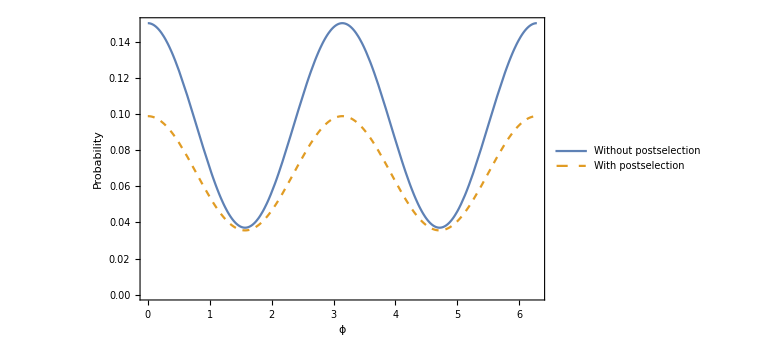

```mathematica
ClearAll[𝓇,ξ]
𝓇=0.5;
ξ=1;
Plot[{wopostselect2[ϕ,𝓇,ξ],wpostselect2[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwo2[𝓇,ξ]]<>" , "<>ToString[Vw2[𝓇,ξ]]<>")"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

## 3. Two-Mode Squeezed Vacuum Input and observing interference for P(coincidence w/o PNR) = P(not 0,not 0) = P(any,any)-P(0,any)-P(any,0)+P(0,0)

```mathematica
ClearAll[outcoin,n]
n=5;
outcoin[ca2_,cb3_]=1/Cosh[ξ] Sum[(-Tanh[ξ]/1 ca0 cb0)^k/k!,{k,0,n}];
(* Approximation of taking only a few terms *)
ClearAll[wopscoin,wpscoin,a,b,c,d]
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
(*c=1; (* amplitude for mode c chosen to observe the interference  *)
d=1;(* amplitude for mode d chosen to observe the interference  *)*)
Prob[n_,ξ_]=Sech[ξ]^2(1-Tanh[ξ]^(2(n+1)))/(1-Tanh[ξ]^2);
wopscoin[ϕ_,𝓇_,ξ_]=Module[{ψp,ψ,P},
𝓉=√(1-𝓇^2);
ψp=CoefficientList[outcoin[ca,cb],{cc3,cd3,ca,cb,cadump,cbdump}];
ψ =Table[√((i-1)!(j-1)!(k-1)!(l-1)!(g-1)!(h-1)!)ψp[[i,j,k,l,g,h]],{i,1,Dimensions[ψp][[1]]},{j,1,Dimensions[ψp][[2]]},{k,1,Dimensions[ψp][[3]]},{l,1,Dimensions[ψp][[4]]},{g,1,Dimensions[ψp][[5]]},{h,1,Dimensions[ψp][[6]]}];
P=Table[Total[Table[Abs[ψ[[i,j]][[k,l,g,h]]]^2,{k,1,Dimensions[ψ[[i,j]]][[1]]},{l,1,Dimensions[ψ[[i,j]]][[2]]},{g,1,Dimensions[ψ[[i,j]]][[3]]},{h,1,Dimensions[ψ[[i,j]]][[4]]}],4],{i,1,Dimensions[ψ][[1]]},{j,1,Dimensions[ψ][[2]]}];
(Total[P,2]-Total[P,{1}][[1]]-Total[P,{2}][[1]]+P[[1,1]])/Prob[n,ξ]
];
wpscoin[ϕ_,𝓇_,ξ_]=Module[{ψp,ψ,P},
𝓉=√(1-𝓇^2);
ψp=CoefficientList[outcoin[ca,cb],{cc3,cd3,ca,cb,cadump,cbdump}];
ψ =Table[√((i-1)!(j-1)!(k-1)!(l-1)!(g-1)!(h-1)!)ψp[[i,j,k,l,g,h]],{i,1,Dimensions[ψp][[1]]},{j,1,Dimensions[ψp][[2]]},{k,1,Dimensions[ψp][[3]]},{l,1,Dimensions[ψp][[4]]},{g,1,Dimensions[ψp][[5]]},{h,1,Dimensions[ψp][[6]]}];
P=Table[Total[Table[Abs[ψ[[i,j]][[a+1,b+1,g,h]]]^2,{g,1,Dimensions[ψ[[i,j]][[a+1,b+1]]][[1]]},{h,1,Dimensions[ψ[[i,j]][[a+1,b+1]]][[2]]}],2],{i,1,Dimensions[ψ][[1]]},{j,1,Dimensions[ψ][[2]]}];
(Total[P,2]-Total[P,{1}][[1]]-Total[P,{2}][[1]]+P[[1,1]])/Prob[n,ξ]
];
(* Visibility *)
Vwocoin[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wopscoin [0,𝓇,ξ];
Imin =wopscoin [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vwcoin[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wpscoin [0,𝓇,ξ];
Imin =wpscoin [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
```

```mathematica
Plot[{Vwocoin[0.9,ξ],Vwocoin[0.7,ξ],Vwocoin[0.5,ξ],Vwocoin[0.3,ξ],Vwocoin[0.1,ξ]},{ξ,0.01,4},PlotRange->Full,GridLines->{{},{}},Frame->True,FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopscoin[0,0.9,ξ],wopscoin [0,0.7,ξ],wopscoin[0,0.5,ξ],wopscoin[0,0.3,ξ],wopscoin[0,0.1,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},GridLines->{{},{}},LabelStyle->Large,ImageSize->Scaled[0.30]]
```

-Graphics-

-Graphics-

```mathematica
ClearAll[𝓇,ξ]
𝓇=0.5;
ξ=0.5;
Plot[{wopscoin[ϕ,𝓇,ξ],wpscoin[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwocoin[𝓇,ξ]]<>" , "<>ToString[Vwcoin[𝓇,ξ]]<>")"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

-Graphics-

## SMSV Wigner function

## Wigner function

Convention: α =  (a+ⅈ b)/(√2) ⇒ a = √2 Re[ α]

### Number State

```mathematica
Wn[a_,b_,n_]:= 1/π(-1)^n LaguerreL[n,2(a^2+b^2)] ⅇ^(-(a^2+b^2));
```

### SMSV Exact

```mathematica
Wsqueezed[x_,p_,s_]:=1/π ⅇ^(-s x^2- p^2/s);
Plot3D[Wsqueezed[x,p,3],{x,-3.5,3.5},{p,-3.5,3.5},PlotRange->Full,PlotPoints->25,Mesh->Automatic, ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],AxesLabel->Automatic,LabelStyle->Large]
```

### SMSV Approx. using few number states

#### Check: Assuming that the Wigner function is a linear transformation (It is not)

```mathematica
Wsqa[a_,b_,ξ_,n_]:=1/(√Cosh[ξ])∑_(k=0)^n √Binomial[2k,k] Wn[a,b,2k](-Tanh[ξ]/2)^k;
Plot3D[Wsqa[x,p,3,10],{x,-3.5,3.5},{p,-3.5,3.5},PlotRange->Full,PlotPoints->25,Mesh->Automatic, ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->Automatic,LabelStyle->Large]
```

This shows that Wigner function is not a linear transformation.

### Calculation of the Wigner function from the pure squeezed state wave function

```mathematica
ψsq[s_,x_]:=(s/π)^(1/4)ⅇ^(-s/2 x^2);
Wsqcal[s_,x_,p_]:=1/(2π)NIntegrate[ⅇ^(ⅈ p y)Conjugate[(ψsq[s,x-1/2 y])] ψsq[s,x+1/2 y],{y,-100,100}];
(*Plot3D[Wsqcal[0.5,a,b],{a,-3.5,3.5},{b,-3.5,3.5},PlotRange->Full,PlotPoints->25,Mesh->Automatic, ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full]*)
```

```mathematica
ClearAll[limits,range,s]
limits=3.5;
range=10;
s=3;
matWsqcal=Table[Re[Chop[Wsqcal[s,(x-1)limits/range-limits,(p-1)limits/range-limits]]],{p,1,2 range +1},{x,1,2 range +1}];

ListPlot3D[matWsqcal,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->Automatic, ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p},LabelStyle->Large]
ClearAll[limits,range,s]
```

### Calculation of the Wigner function using number states (and approx. by taking few terms)

```mathematica
ψn[n_,x_]=(ⅇ^(-x^2/2))/(π^(1/4)√(n!2^n))HermiteH[n,x];
ψsqapprox[ξ_,nlim_,x_]=1/(√Cosh[ξ])∑_(k=0)^nlim √Binomial[2k,k](-Tanh[ξ]/2)^k ψn[2k,x];
nlim=5;
Wsqapprox[ξ_,nlim_,x_,p_]:=1/(2π)NIntegrate[ⅇ^(ⅈ p y)Conjugate[(ψsqapprox[ξ,nlim,x-1/2 y])] ψsqapprox[ξ,nlim,x+1/2 y],{y,-50,50}];
ClearAll[limits,range,ξ,s]
limits=3.5;
range=10;
s=3;
ξ=1/2 Log[s];
matWsqapprox=Table[Re[Chop[Wsqapprox[ξ,nlim,(x-1)limits/range-limits,(p-1)limits/range-limits]]],{p,1,2 range +1},{x,1,2 range +1}];

ListPlot3D[matWsqapprox,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->Automatic,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p},LabelStyle->Large]
ClearAll[limits,range,ξ,s]
```

## SMSV → NA → Homodyne

## Setup

#### Beam splitter transformation

```mathematica
B[r_,t_]={{t,-r},{r,t}};
```

```mathematica
(* Creation operators are representated by c *)
```

#### NA

```mathematica
{ca0,cb0}=B[𝓇,𝓉].{ca,cb};
```

### Input State: SMSV

```mathematica
S[ξ_,n_]=1/(√Cosh[ξ])∑_(k=0)^n √Binomial[2k,k](-Tanh[ξ]/2)^k ca0^(2k)/(√((2k)!));
```

```mathematica
b=0;(* Post selection *)
coeff[ξ_,nlim_]:=CoefficientList[S[ξ,nlim],{cb,ca}];
ψout[ξ_,nlim_,x_]:=Total[Table[√(b!(i-1)!)coeff[ξ,nlim][[b+1,i]]ψn[i-1,x],{i,1,Dimensions[coeff[ξ,nlim]][[2]]}]];
```

```mathematica
ClearAll[𝓇,𝓉]
𝓇=0.5;
𝓉=√(1-𝓇^2);
nlim=5;
W[ξ_,nlim_,x_,p_]:=1/(2π)NIntegrate[ⅇ^(ⅈ p y)Conjugate[(ψout[ξ,nlim,x-1/2 y])] ψout[ξ,nlim,x+1/2 y],{y,-50,50}];
ClearAll[limits,range,ξ,s]
limits=3.5;
range=10;
s=3;
ξ=1/2 Log[s];
wpsmat=Table[Re[Chop[W[ξ,nlim,(x-1)limits/range-limits,(p-1)limits/range-limits]]],{p,1,2 range +1},{x,1,2 range +1}];

ListPlot3D[wpsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->Automatic,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p},LabelStyle->Large]
ClearAll[limits,range,ξ,s]
ClearAll[𝓇,𝓉]
```

-Graphics3D-

## Is the attenuation noiseless? SMSV → Attenuation (w/o post selection) →Homodyne

## Setup

#### Beam splitter transformation

```mathematica
B[r_,t_]={{t,-r},{r,t}};
```

```mathematica
(* Creation operators are representated by c *)
```

#### NA

```mathematica
{ca0,cb0}=B[𝓇,𝓉].{ca,cb};
```

### Input State: SMSV

```mathematica
S[ξ_,n_]=1/(√Cosh[ξ])∑_(k=0)^n √Binomial[2k,k](-Tanh[ξ]/2)^k ca0^(2k)/(√((2k)!));
```

```mathematica
b=0;(* Post selection *)
coeff[ξ_,nlim_]:=CoefficientList[S[ξ,nlim],{cb,ca}];
ψout[ξ_,nlim_,x_]:=Module[{coefftable},
coefftable=coeff[ξ,nlim];
Table[Total[Table[√((i-1)!(j-1)!)coefftable[[i,j]]ψn[j-1,x],{j,1,Dimensions[coefftable][[2]]}]],{i,1,Dimensions[coefftable][[1]]}]
];
```

```mathematica
ClearAll[𝓇,𝓉]
𝓇=0.5;
𝓉=√(1-𝓇^2);
nlim=5;
wopsW[ξ_,nlim_,x_,p_]:=Module[{coefftable,dim,Pr},
coefftable=coeff[ξ,nlim];
dim=Dimensions[coefftable];
Pr=Table[Abs[√((i-1)!(j-1)!)coefftable[[i,j]]]^2,{i,1,dim[[1]]},{j,1,dim[[2]]}];
Total[Table[(Total[Pr,{2}][[i]])/(2π)NIntegrate[ⅇ^(ⅈ p y)Conjugate[(ψout[ξ,nlim,x-1/2 y][[i]])] ψout[ξ,nlim,x+1/2 y][[i]],{y,-50,50}],{i,1,dim[[1]]}]]
];
ClearAll[limits,range,ξ,s]
limits=3.5;
range=10;
s=3;
ξ=1/2 Log[s];
wopsmat=Table[Re[Chop[wopsW[ξ,nlim,(x-1)limits/range-limits,(p-1)limits/range-limits]]],{p,1,2 range +1},{x,1,2 range +1}];

ListPlot3D[wopsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->Automatic,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p},LabelStyle->Large]
ClearAll[limits,range,ξ,s]
ClearAll[𝓇,𝓉]
```

## Model fitting

### Before

```mathematica
model=a Exp[(-(s x^2+p^2/s))/(2 σ^2)];
range =(Dimensions[matWsqapprox][[1]]-1)/2;
```

```mathematica
IdxData= Table[{i-range -1,j-range-1,matWsqapprox[[i,j]]},{i,1,2range+1},{j,1,2range+1}];
Data=Flatten[IdxData,1];
fit = FindFit[Data,model,{{a,0.5},σ,s},{p,x}]
```

{a→0.318252,σ→2.02043,s→2.9934}

### After (attenuation w/ post selection)

```mathematica
model=a Exp[(-(s x^2+p^2/s))/(2 σ^2)];
range =(Dimensions[wpsmat][[1]]-1)/2;
IdxData= Table[{i-range -1,j-range-1,wpsmat[[i,j]]},{i,1,2range+1},{j,1,2range+1}];
Data=Flatten[IdxData,1];
fit = FindFit[Data,model,{{a,0.5},σ,s},{p,x}]
```

{a→0.297363,σ→2.02031,s→2.19978}

### After (attenuation w/o post selection)

```mathematica
model=a Exp[(-(s x^2+p^2/s))/(2 σ^2)];
range =(Dimensions[wopsmat][[1]]-1)/2;
IdxData= Table[{i-range -1,j-range-1,wopsmat[[i,j]]},{i,1,2range+1},{j,1,2range+1}];
Data=Flatten[IdxData,1];
fit = FindFit[Data,model,{{a,0.5},σ,s},{p,x}]
```

{a→0.277011,σ→2.02633,s→2.20025}

## Cat States through noiseless attenuation

### Calculation of the Wigner function using number states (and approx. by taking few terms)

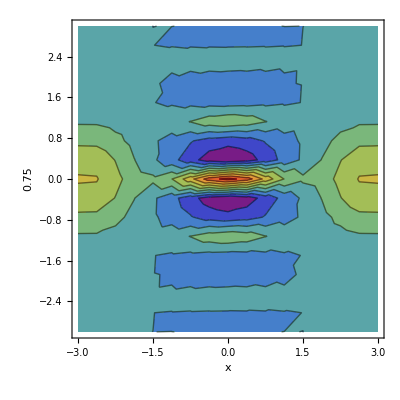

```mathematica
ψn[n_,x_]=(ⅇ^(-x^2/2))/(π^(1/4)√(n!2^n))HermiteH[n,x];
ψc[α_,nlim_,x_]=ⅇ^((-Abs[α]^2)/2)∑_(n=0)^nlim (α^n ψn[n,x])/(√(n!));
ψcExact[α_,nlim_,x_]=1/π^(1/4)ⅇ^((-(x-√2 α)^2)/2);
ψCat[α_,nlim_,x_]=(ψc[α,nlim,x]+ψc[-α,nlim,x])/(√2);
nlim=20;
WCat[α_,nlim_,x_,p_]:=1/(2π)NIntegrate[ⅇ^(ⅈ p y)Conjugate[(ψCat[α,nlim,x-1/2 y])] ψCat[α,nlim,x+1/2 y],{y,-50,50}];
WCatExact[α_,nlim_,x_,p_]:=(ⅇ^(-(x-√2 α)^2-p^2)+ⅇ^(-(x+√2 α)^2-p^2)+ⅇ^(-x^2-p^2)Cos[2 √2 α p]);
ClearAll[limits,range,α,s]
limits=3;
range=8;
α=2;
matCat=Table[Re[Chop[WCat[α,nlim,(x-1)limits/range-limits,(p-1)limits/range-limits]]],{p,1,2 range +1},{x,1,2 range +1}];
ListContourPlot[matCat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->Automatic,ColorFunction->"Rainbow",PlotRange->Full,AxesLabel->{x,p},LabelStyle->Large]
ClearAll[limits,range,α]
```

```mathematica
ListPlot3D[matCat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->Automatic,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p},LabelStyle->Large]
ClearAll[limits,range,α]
```

### Calculation of the Wigner function using number states (and approx. by taking few terms) after noiseless attenuation

#### Beam splitter transformation

```mathematica
B[r_,t_]={{t,-r},{r,t}};
```

```mathematica
(* Creation operators are representated by c *)
```

#### NA

```mathematica
{ca0,cb0}=B[𝓇,𝓉].{ca,cb};
```

```mathematica
ψn[n_,x_]=(ⅇ^(-x^2/2))/(π^(1/4)√(n!2^n))HermiteH[n,x];
ψin[α_,n_]=1/(√2)(ⅇ^((-Abs[α]^2)/2)∑_(n=0)^nlim ((α^n +(-α)^n)ca0^n)/(n!));
```

```mathematica
b=0;(* Post selection *)
α=2;
nlim=20;
coefftable=CoefficientList[ψin[α,nlim],{cb,ca}];
Pr=Chop[Table[Abs[√((i-1)!   (j-1)!)coefftable[[i,j]]]^2,{i,1,Dimensions[coefftable][[1]]},{j,1,Dimensions[coefftable][[2]]}]];
```

```mathematica
Dimensions[coefftable]
```

{21,21}

#### w/ post selection

```mathematica
ψoutwps[x_]=FullSimplify[Total[Table[√(b!(i-1)!)coefftable[[b+1,i]]ψn[i-1,x],{i,1,Dimensions[coefftable][[2]]}]]];
```

#### results

```mathematica
𝓇=0.5;
𝓉=√(1-𝓇^2);
Wwps[x_,p_]:=1/(Total[Pr,{2}][[b+1]]2π)NIntegrate[ⅇ^(ⅈ p y)Conjugate[(ψoutwps[x-1/2 y])] ψoutwps[x+1/2 y],{y,-20,20}];
```

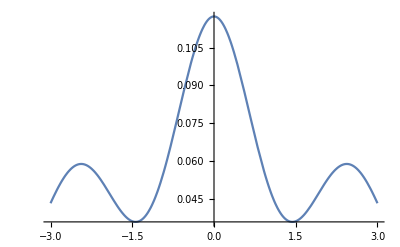

```mathematica
Plot[Wwps[x,0],{x,-3,3}]
```

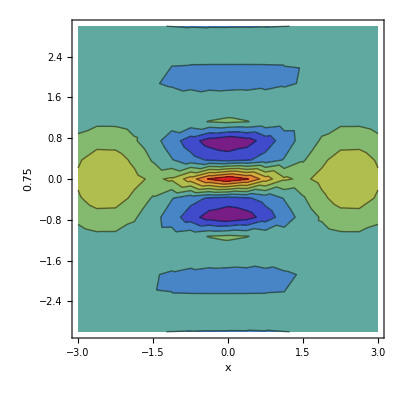

```mathematica
limits=3;
range=8;
wpsmat=Table[Re[Chop[Wwps[(x-1)limits/range-limits,(p-1)limits/range-limits]]],{p,1,2 range +1},{x,1,2 range +1}];
ListContourPlot[wpsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->Automatic,ColorFunction->"Rainbow",PlotRange->Full,AxesLabel->{x,p},LabelStyle->Large]
ClearAll[𝓇,𝓉]
```

```mathematica
ListPlot3D[wpsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->Automatic,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p},LabelStyle->Large]
ClearAll[𝓇,𝓉]
```

#### w/o post selection

```mathematica
ψoutwops[x_]=Table[Total[Table[√((i-1)!(j-1)!)coefftable[[i,j]]ψn[j-1,x],{j,1,Dimensions[coefftable][[2]]}]],{i,1,Dimensions[coefftable][[1]]}];
```

```mathematica
Dimensions[ψoutwops[x]]
```

{21}

#### results

```mathematica
𝓇=0.5;
𝓉=√(1-𝓇^2);
Wwops[x_,p_]:=Total[Table[(Total[Pr,{2}][[i]])/(2π)NIntegrate[ⅇ^(ⅈ p y)Conjugate[(ψoutwops[x-1/2 y][[i]])] ψoutwops[x+1/2 y][[i]],{y,-20,20}],{i,Dimensions[coefftable][[1]]}]];
```

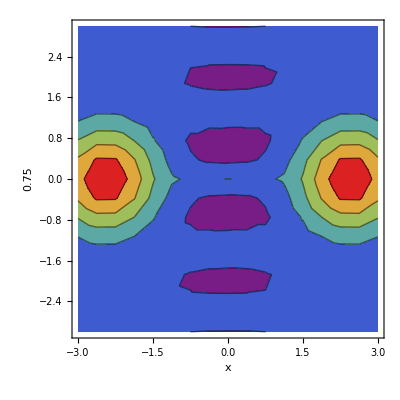

```mathematica
limits=3;
range=8;
wpsmat=Table[Re[Chop[Wwops[(x-1)limits/range-limits,(p-1)limits/range-limits]]],{p,1,2 range +1},{x,1,2 range +1}];
ListContourPlot[wpsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->Automatic,ColorFunction->"Rainbow",PlotRange->Full,AxesLabel->{x,p},LabelStyle->Large]
```

```mathematica
ListPlot3D[wpsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->Automatic,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p},LabelStyle->Large]
```

```mathematica
pr=Total[Pr,{2}];
Total[pr]
pr//MatrixForm
```

```mathematica
Total[Pr,{2}][[4]]
```

1.00034

(0.368791
0.366968
0.184396
0.0611613
0.0153663
0.00305806
0.00051221
0.0000728109
9.14656×10^-6
1.01124×10^-6
1.01617×10^-7
9.13922×10^-9
6.02235×10^-10
0
0
0
0
0
0
0
0)

### Model fitting

```mathematica
model=A(ⅇ^(-(x-√2 α)^2-p^2)+ⅇ^(-(x+√2 α)^2-p^2)+ⅇ^(-x^2-p^2)Cos[2 √2 α p]);
```